# Numerical MST Scattering Phase Algorithm

## Setup

Loading relevant BHPT paclets.

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
Needs["KerrGeodesics`"]
Needs["Teukolsky`"]
```

Generating a vector of values of  to run the algorithm on. Start with a value slightly higher than zero as the algorithm has trouble converging as .

```mathematica
ϵ0ValsStart=0.02`32;
ϵ0ValsEnd=1.8`32;
ϵ0ValsPoints=80;
ϵ0ValsStep=(ϵ0ValsEnd-ϵ0ValsStart)/ϵ0ValsPoints;
ϵ0Vals=Table[x,{x,ϵ0ValsStart,ϵ0ValsEnd,ϵ0ValsStep}]
```

{0.02,0.04225,0.0645,0.08675,0.109,0.13125,0.1535,0.17575,0.198,0.22025,0.2425,0.26475,0.287,0.30925,0.3315,0.35375,0.376,0.39825,0.4205,0.44275,0.465,0.48725,0.5095,0.53175,0.554,0.57625,0.5985,0.62075,0.643,0.66525,0.6875,0.70975,0.732,0.75425,0.7765,0.79875,0.821,0.84325,0.8655,0.88775,0.91,0.93225,0.9545,0.97675,0.999,1.02125,1.0435,1.06575,1.088,1.11025,1.1325,1.15475,1.177,1.19925,1.2215,1.24375,1.266,1.28825,1.3105,1.33275,1.355,1.37725,1.3995,1.42175,1.444,1.46625,1.4885,1.51075,1.533,1.55525,1.5775,1.59975,1.622,1.64425,1.6665,1.68875,1.711,1.73325,1.7555,1.77775}

Defining precalculated expansions of relevant parameters to compare against the numerical result later.

```mathematica
ν000Expansion[q_,ϵ_]:=-7/6*ϵ^2+(-9449/7560+3q^2/35)ϵ^4 (*s, l, m = 0*)
```

```mathematica
ν220Expansion[q_,ϵ_]:=2-107/210*ϵ^2+(-1695233+404250 q^2)/9261000 ϵ^4 (*s = 2, l = 2, m = 0*)
```

```mathematica
phase000Expansion[q_,ϵ_]:=1/2 (-1+2 EulerGamma+2 Log[2]+2 Log[ϵ]) ϵ+((6 ⅈ-6 ⅈ q^2+6 ⅈ √(1-q^2)+11 π √(1-q^2)) ϵ^2)/(12 √(1-q^2))+1/(36 √(1-q^2))(-33+18 ⅈ π+33 q^2-18 ⅈ π q^2+51 √(1-q^2)-36 EulerGamma √(1-q^2)+18 ⅈ π √(1-q^2)+11 π^2 √(1-q^2)+3 q^2 √(1-q^2)-36 √(1-q^2) Log[2]-36 √(1-q^2) Log[√(1-q^2) ϵ]-12 √(1-q^2) Zeta[3]) ϵ^3 (*s, l, m = 0*)
```

```mathematica
phase010Expansion[q_,ϵ_]:=1/2 (-3+2 EulerGamma+2 Log[2]+2 Log[ϵ]) ϵ+(19 π ϵ^2)/60+1/180 (19 π^2-9 q^2-60 Zeta[3]) ϵ^3 (*s = 0, l = 1, m = 0*)
```

```mathematica
phase110Expansion[q_,ϵ_]:=1/4 (-5+4 EulerGamma+4 Log[2]+4 Log[ϵ]) ϵ+1/240 (94 π-15 ⅈ q^2) ϵ^2+((105+188 π^2-180 q^2-480 Zeta[3]) ϵ^3)/1440 (*s = 1, l = 1, m = 0*)
```

```mathematica
phase220Expansion[q_,ϵ_]:=1/3 (-5+3 EulerGamma+3 Log[2]+3 Log[ϵ]) ϵ+(107 π ϵ^2)/420+((-1015+1926 π^2-945 q^2-7560 Zeta[3]) ϵ^3)/22680 (*s = 2, l = 2, m = 0*)
```

## Numerical Phase Algorithm Module

The main numerical scattering phase module. The module takes as input:
- n: To what order we want appropriate MST coefficients while calculating the phase. A recommended value is around 10.
- nUp: How many higher raising ratios we want to determine the n-th MST coefficient. Helps with stability. Recommended value is around 5.
- s: The spin of the perturbation. Note that if the final goal is calculate the phase for some positive , say 2, you should input -2 here as the intermediate step in determining  requires the sign of  to be flipped.
- l, m: Integers enumerating the basis of solutions of the Teukolsky equation.
- q: The black hole spin parameter.
- : the value of  we are evaluating the phase for.
The calculation is carried out by recovering the numerical value for  using BHPT’s Teukolsky paclet’s RenormalizedAngularMomentum function, determining the lowest n + nUp (not n for stability) indexed raising ratios with R[n + 6] set to zero, getting the MST coefficients from them, then finally inserting these into the appropriate formulas to get the scattering phase.

```mathematica
expPhase[n_,nUp_,s_,l_,m_,q_,ϵ_]:=Module[{α,β,γ,κ,τ,λ,negλ,ν,ii,Ri,R,an,Aplus,Aminus,Knu,aNegNuNeg1,KNegNuNeg1,ω,BreflOverBinc,Cstar,expPhaseVal},
α[i_]:=I*ϵ*κ*(i+ν+1+s+I*ϵ)*(i+ν+1+s-I*ϵ)*(i+ν+1+I*τ)/((i+ν+1)*(2*i+2*ν+3));
β[i_]:=-λ-s*(s+1)+(i+ν)*(i+ν+1)+ϵ^2+ϵ*(ϵ-m*q)+ϵ*(ϵ-m*q)*(s^2+ϵ^2)/((i+ν)*(i+ν+1)) ;
γ[i_]:=-I*ϵ*κ*(i+ν-s+I*ϵ)*(i+ν-s-I*ϵ)*(i+ν-I*τ)/((i+ν)*(2i+2ν-1));
κ=Sqrt[1-q^2];
τ=(ϵ-m*q)/κ;
λ=SpinWeightedSpheroidalEigenvalue[s,l,m,q*ϵ/2];
negλ=SpinWeightedSpheroidalEigenvalue[-s,l,m,q*ϵ/2];
ν=RenormalizedAngularMomentum[s,l,m,q,ϵ/2];
For[ii=n+nUp,ii>=1,ii--,
If[ii==n+nUp,
Ri=-γ[ii]/β[ii],
Ri=-γ[ii]/(β[ii]+α[ii]*R[ii+1])];
R[ii]=Ri];
an[0]=1;
an[1]=R[1];
For[ii=2,ii<=n,ii++,
an[ii]=(-β[ii-1]*an[ii-1]-γ[ii-1]*an[ii-2])/α[ii-1]];
For[ii=-1,ii>=-n,ii--,
an[ii]=(-β[ii+1]*an[ii+1]-α[ii+1]*an[ii+2])/γ[ii+1]];
Aplus=E^(-Pi/2*ϵ)*E^(Pi/2*I*(ν+1-s))*2^(-1+s-I*ϵ)*Gamma[ν+1-s+I*ϵ]/Gamma[ν+1+s-I*ϵ]*Sum[an[ii],{ii,-n,n}];
Aminus=2^(-1-s+I*ϵ)*E^(-I*Pi/2*(ν+1+s))*E^(-Pi*ϵ/2)*Sum[(-1)^ii*Pochhammer[ν+1+s-I*ϵ,ii]/Pochhammer[ν+1-s+I*ϵ,ii]*an[ii],{ii,-n,n}];
Knu=E^(I*ϵ*κ)*(2*ϵ*κ)^(s-ν)*2^(-s)*Gamma[1-s-2*I*(ϵ+τ)/2]*Gamma[2ν+2]/(Gamma[ν+1-s+I*ϵ]*Gamma[ν+1+I*τ]*Gamma[ν+1+s+I*ϵ])*Sum[(-1)^ii*Gamma[ii+2ν+1]/ii!*Gamma[ii+ν+1+s+I*ϵ]/Gamma[ii+ν+1-s-I*ϵ]*Gamma[ii+ν+1+I*τ]/Gamma[ii+ν+1-I*τ]*an[ii],{ii,0,n}]/Sum[(-1)^ii/((-ii)!*Pochhammer[2ν+2,ii])*Pochhammer[ν+1+s-I*ϵ,ii]/Pochhammer[ν+1-s+I*ϵ,ii]*an[ii],{ii,-n,0}];
For[ii=-n,ii<=n,ii++,aNegNuNeg1[-ii]=an[ii]];
KNegNuNeg1=E^(I*ϵ*κ)*(2*ϵ*κ)^(s-(-ν-1))*2^(-s)*Gamma[1-s-2*I*(ϵ+τ)/2]*Gamma[2(-ν-1)+2]/(Gamma[(-ν-1)+1-s+I*ϵ]*Gamma[(-ν-1)+1+I*τ]*Gamma[(-ν-1)+1+s+I*ϵ])*Sum[(-1)^ii*Gamma[ii+2(-ν-1)+1]/ii!*Gamma[ii+(-ν-1)+1+s+I*ϵ]/Gamma[ii+(-ν-1)+1-s-I*ϵ]*Gamma[ii+(-ν-1)+1+I*τ]/Gamma[ii+(-ν-1)+1-I*τ]*aNegNuNeg1[ii],{ii,0,n}]/Sum[(-1)^ii/((-ii)!*Pochhammer[2(-ν-1)+2,ii])*Pochhammer[(-ν-1)+1+s-I*ϵ,ii]/Pochhammer[(-ν-1)+1-s+I*ϵ,ii]*aNegNuNeg1[ii],{ii,-n,0}];
ω=ϵ/2;
BreflOverBinc=ω^(-2s)*E^(-I*ϵ(1-κ))*E^(2*I*ϵ*Log[ϵ])*(Knu+I*E^(I*Pi*ν)*KNegNuNeg1)/(Knu-I*E^(-I*Pi*ν)*Sin[Pi*(ν-s+I*ϵ)]/Sin[Pi*(ν+s-I*ϵ)]*KNegNuNeg1)*Aminus/Aplus;
If[s==0,
Cstar=1,
If[s==-1,
Cstar=Sqrt[(negλ+2+q^2*ω^2-2m*q*ω)^2+4*m*q*ω-4q^2*ω^2],
Cstar=(((λ+2)^2+4q*m*ω-4*q^2*ω^2)*(λ^2+36q*m*ω-36q^2*ω^2)+(2λ+3)*(96q^2*ω^2-48q*ω*m)-144ω^2*q^2)^(1/2)-12I*ω]];
expPhaseVal=(-1)^(l+1)*Cstar/(2ω)^(-2s)*BreflOverBinc;
expPhaseVal]
```

## Comparisons Between Expansion and Numerics

Example comparisons are made below for s = 0, l = 0, m = 0.

```mathematica
n=10;
nUp=5;
```

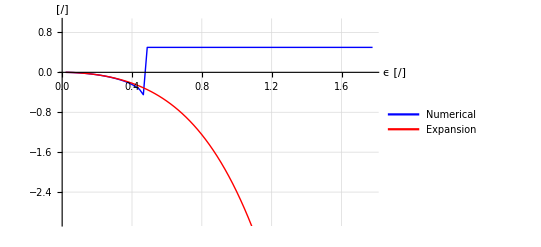

```mathematica
plotNuI=ListLinePlot[Table[{ϵ0,Re[RenormalizedAngularMomentum[0,0,0,0.5`32,ϵ0/2]]},{ϵ0,ϵ0Vals}],PlotStyle->{Blue,Thickness[0.0025]},GridLines->Automatic,AxesLabel->{"ϵ [/]"," [/]"}];
plotNuII=ListLinePlot[Table[{ϵ0,ν000Expansion[0.5`32,ϵ0]},{ϵ0,ϵ0Vals}],PlotStyle->{Red,Thickness[0.0025]},GridLines->Automatic,AxesLabel->{"ϵ [/]"," [/]"}];
plotNu=Show[plotNuI,plotNuII,PlotRange->{-3,1}];
plotNuLegended=Legended[plotNu,LineLegend[{Blue,Red},{"Numerical","Expansion"}]]
```

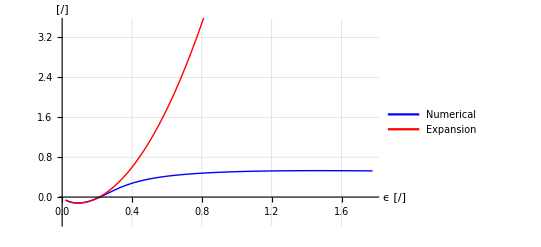

```mathematica
plotExpI=ListLinePlot[Table[{ϵ0,Re[1/(2I)*Log[expPhase[n,nUp,0,0,0,0.5`32,ϵ0]]]},{ϵ0,ϵ0Vals}],PlotStyle->{Blue,Thickness[0.0025]},GridLines->Automatic,AxesLabel->{"ϵ [/]"," [/]"}];
plotExpII=ListLinePlot[Table[{ϵ0,Re[phase000Expansion[0.5`32,ϵ0]]},{ϵ0,ϵ0Vals}],PlotStyle->{Red,Thickness[0.0025]},GridLines->Automatic,AxesLabel->{"ϵ [/]"," [/]"}];
plotExp=Show[plotExpI,plotExpII,PlotRange->{-0.5,3.5}];
plotExpLegended=Legended[plotExp,LineLegend[{Blue,Red},{"Numerical","Expansion"}]]
```

## (Extra) MST Coefficients Module

A module calculating only the nn-th MST coefficient. Useful in seeing if the main module is converging properly, and to guide the choice of n and nUp. Except nn, the other inputs are the same as before.

```mathematica
ann[n_,nn_,nUp_,s_,l_,m_,q_,ϵ_]:=Module[{α,β,γ,κ,τ,λ,ν,ii,Ri,R,an},
α[i_]:=I*ϵ*κ*(i+ν+1+s+I*ϵ)*(i+ν+1+s-I*ϵ)*(i+ν+1+I*τ)/((i+ν+1)*(2*i+2*ν+3));
β[i_]:=-λ-s*(s+1)+(i+ν)*(i+ν+1)+ϵ^2+ϵ*(ϵ-m*q)+ϵ*(ϵ-m*q)*(s^2+ϵ^2)/((i+ν)*(i+ν+1)) ;
γ[i_]:=-I*ϵ*κ*(i+ν-s+I*ϵ)*(i+ν-s-I*ϵ)*(i+ν-I*τ)/((i+ν)*(2i+2ν-1));
κ=Sqrt[1-q^2];
τ=(ϵ-m*q)/κ;
λ=SpinWeightedSpheroidalEigenvalue[s,l,m,q*ϵ/2];
ν=RenormalizedAngularMomentum[s,l,m,q,ϵ/2];
For[ii=n+nUp,ii>=1,ii--,
If[ii==n+nUp,
Ri=-γ[ii]/β[ii],
Ri=-γ[ii]/(β[ii]+α[ii]*R[ii+1])];
R[ii]=Ri];
an[0]=1;
an[1]=R[1];
For[ii=2,ii<=n,ii++,
an[ii]=(-β[ii-1]*an[ii-1]-γ[ii-1]*an[ii-2])/α[ii-1]];
For[ii=-1,ii>=-n,ii--,
an[ii]=(-β[ii+1]*an[ii+1]-α[ii+1]*an[ii+2])/γ[ii+1]];
an[nn]]
```

An example plot showing the swift convergence of an MST coefficient for s, l, m = 0 as the order we determine it to, n, increases.

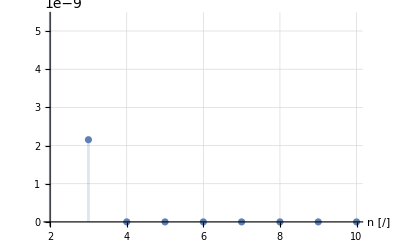

```mathematica
DiscretePlot[Abs[ann[n+1,2,1,0,0,0,0.5`32,0.3`32]-ann[n,2,1,0,0,0,0.5`32,0.3`32]]/Abs[ann[n,2,5,0,0,0,0.5,0.3]],{n,{2,3,4,5,6,7,8,9,10}},GridLines->Automatic,AxesLabel->{"n [/]", ""}]
```